```mathematica
ReverseSort@Last@With[{n=100,m=0},NestList[Block[{x=#},Scan[(If[x[[#]]>0,x[[#]]--;With[{j=RandomChoice[Delete[Range@n,#]]},x[[j]]++]])&,Range@n];x]&,ConstantArray[n,n],m]]
```

Append[{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}]

```mathematica
distbyRound=Parallelize[With[{n=10,m=1000},NestList[Block[{x=#},Scan[(If[x[[#]]>0,x[[#]]--;With[{j=RandomChoice[Delete[Range@n,#]]},x[[j]]++]])&,Range@n];x]&,ConstantArray[n,n],m]]];ReverseSort@Last@distbyRound
```

Parallelize::nopar1: With[{n=10,m=1000},NestList[Block[{x=#1},Scan[If[«2»]&,Range[n]];x]&,ConstantArray[n,n],m]] cannot be parallelized; proceeding with sequential evaluation.

{29,25,17,10,9,4,3,2,1,0}

```mathematica
Manipulate[TableForm[{BarChart[distbyRound[[x]],AxesLabel->{"Player","Dollar Amount"},ChartLayout->"Stacked"],BarChart[distbyRound[[x]],AxesLabel->{"Player","Dollar Amount"},ChartLayout->"Stacked"]}],{x,1,Length@distbyRound,10}]
```

```mathematica
BarChart[distbyRound,AxesLabel->{"Player","Dollar Amount"},ChartLayout->"Stacked"]
```

```mathematica
Manipulate[BarChart[distbyRound[[x]],AxesLabel->{"Player","Dollar Amount"},ChartLayout->"Stacked"],{x,1,Length@distbyRound,10}]
```

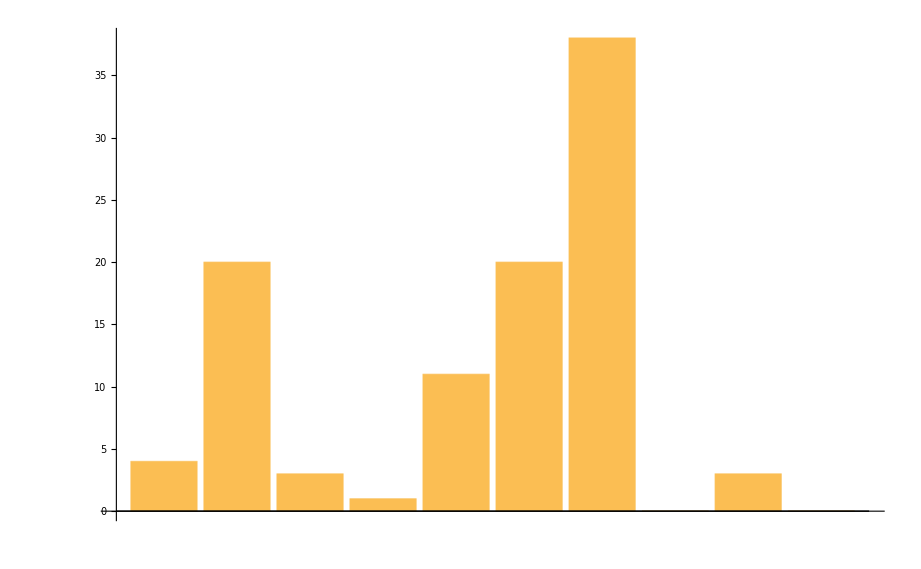

```mathematica
BarChart@Last@distbyRound
```

```mathematica
distbyPlayer=Transpose[distbyRound[[All,1;;10]]]
```

{1}
 |  |  |  |

```mathematica
Length@distbyPlayer[[1]]
```

Part::partd: Part specification distbyPlayer⟦1⟧ is longer than depth of object.

2

```mathematica
Length@dist
```

1001

```mathematica
Length@Transpose[dist[[1;;3]]]
```

100

```mathematica
ListLinePlot[#&/@distbyPlayer,AxesLabel->{"Round","Dollar Amount"}]
```

-Graphics-

```mathematica
Total@%137[[3]]
```

10000

```mathematica
100*100
```

10000

```mathematica
l={2,3,4}
```

{2,3,4}

```mathematica
Scan[Print[#^2]&,l]
```

4

9

16

```mathematica
l
```

{2,3,4}

```mathematica
Range@90
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}

```mathematica
data=RandomVariate[UniformDistribution[{0,1}],100];
```

```mathematica
QuantilePlot[data,UniformDistribution[{0,1}]]
```

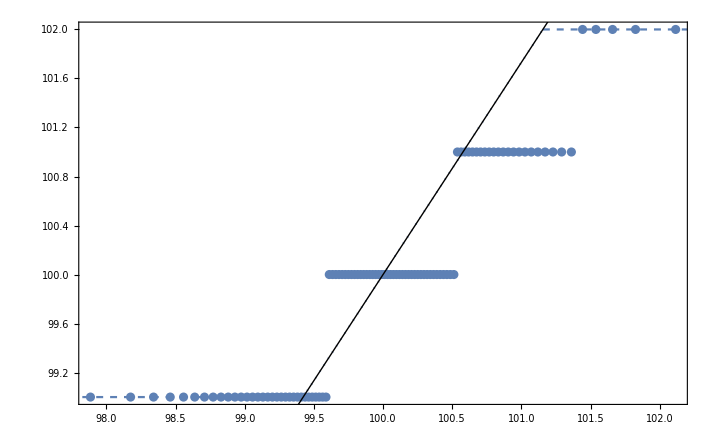

```mathematica
QuantilePlot[dist,UniformDistribution[{0,1}]]
```